# Modelos Matemáticos y Algoritmos - Ejercicio 2

## Jesús Bueno Urbano - 20078941X

Este Mathematica Notebook resume el apartado e) del ejercicio 2 con todas las ordenes que hay que seguir para dibujar los campos vectoriales en los tres casos descritos. Además aprovechamos para poder hacer cálculos tediosos del resto de apartados anteriores, los cuales van antes que el apartado e).

## Planteamiento del sistema

```mathematica
f[u_,v_]=u(1-u-v/(u+B))
g[u_,v_]=v(-C+M*u/(u+B))
```

u (1-u-v/(B+u))

(-C+(M u)/(B+u)) v

## Cálculo y clasificación de los puntos de equilibrio

```mathematica
equilibrio=Solve[{f[u,v]==0,g[u,v]==0},{u,v}]
```

{{u→1,v→0},{u→-(B C)/(C-M),v→-(B (C+B C-M) M)/(C-M)^2},{u→0,v→0}}

```mathematica
P1={u,v}/.equilibrio[[3]]
P2={u,v}/.equilibrio[[1]]
P3={u,v}/.equilibrio[[2]]
```

{0,0}

{1,0}

{-(B C)/(C-M),-(B (C+B C-M) M)/(C-M)^2}

Como vemos, P3 sólo tiene sentido si C < M/(1 + B), que además implica C < M.

```mathematica
DF[{u_,v_}]={{D[f[u,v],u],D[f[u,v],v]},{D[g[u,v],u],D[g[u,v],v]}}
```

{{1-u-v/(B+u)+u (-1+v/(B+u)^2),-u/(B+u)},{(-(M u)/(B+u)^2+M/(B+u)) v,-C+(M u)/(B+u)}}

```mathematica
DF1=DF[P1]
```

{{1,0},{0,-C}}

Como estamos ante una matriz diagonal sabemos que sus valores propios son 1 y - C con direcciones (1, 0) y (0, 1), respectivamente. Luego estamos ante un punto de silla.

```mathematica
DF2=DF[P2]
```

{{-1,-1/(1+B)},{0,-C+M/(1+B)}}

Como estamos ante una matriz triangular superior podemos obtener por simple observación que P2 será Asintóticamente Estable cuando C > M/(1 + B) y un punto de sillaen caso contrario.

```mathematica
FullSimplify[DF3=DF[P3]]
```

{{(2 B C)/(C-M)+((1+B) C)/M,-C/M},{-(1+B) C+M,0}}

```mathematica
FullSimplify[Det[DF3=DF[P3]]]
```

-(C (C+B C-M))/M

Aplicando que M/(1 + B) > C obtenemos que, en caso de existir P3, su estabilidad depende de la traza de la diferencial en este punto ya que su determinante es siempre positivo.

```mathematica
FullSimplify[Tr[DF3=DF[P3]]]
```

(2 B C)/(C-M)+((1+B) C)/M

A continuación nos preguntamos cuándo la traza será negativa, operamos con la expresión y será así si, y sólo si, B > (M - C)/(M + C).

## Órbitas en los ejes

```mathematica
sistema={u'[τ] ==f[u[τ],v[τ]],v'[τ] ==g[u[τ],v[τ]]}
```

{u'[τ]==u[τ] (1-u[τ]-v[τ]/(B+u[τ])),v'[τ]==(-C+(M u[τ])/(B+u[τ])) v[τ]}

```mathematica
ejex=sistema/.{v->Function[τ,0]}
```

{u'[τ]==(1-u[τ]) u[τ],True}

```mathematica
ejey=sistema/.{u->Function[τ,0]}
```

{True,v'[τ]==-C v[τ]}

A partir de aquí comienza el apartado e) propiamente dicho.

## Campos vectoriales

## CASO 1

Ejemplo cuando C > M/(1 + B) :

```mathematica
F1[u_,v_]=u(1-u-v/(u+2));
G1[u_,v_]=v(-2+3*u/(u+2));
equilibrio1=Solve[{F1[u,v]==0,G1[u,v]==0},{u,v}];
P11={u,v}/.equilibrio1[[3]];
P12={u,v}/.equilibrio1[[1]];
P13={u,v}/.equilibrio1[[2]];
```

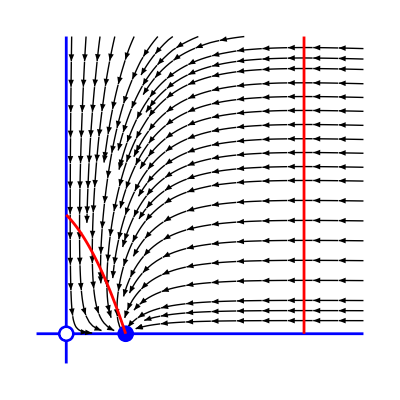

```mathematica
gr01=ParametricPlot[{{t,0},{0,t}},{t,-0.5,5},PlotStyle->{{Blue,Thickness[0.005]},{Blue,Thickness[0.005]}},Axes->False]; (*Ejes*)
gr1=StreamPlot[{F1[u,v],G1[u,v]},{u,0,5},{v,0,5},StreamStyle->Black]; (*Campos vectoriales*)
gr11=ListPlot[{P11,P12},PlotStyle-> {PointSize[0.03],Blue}];
gr12=ListPlot[{P11},PlotStyle-> {PointSize[0.02],White}];
gr13 = ParametricPlot[{4,t},{t,0,5},PlotStyle->{Red,Thickness[0.005]}]; (*Campo vertical*)
gr14 = ParametricPlot[{t,(1-t)*(2+t)},{t,0,1},PlotStyle->{Red,Thickness[0.005]}];(*Campo horizontal*)
Show[gr01,gr1,gr11,gr12,gr13,gr14]
```

## CASO 2

Ejemplo cuando C < M/(1 + B)  y P3 es asintócamente estable:

```mathematica
F2[u_,v_]=u(1-u-v/(u+0.9));
G2[u_,v_]=v(-1+3*u/(u+0.9));
equilibrio2=Solve[{F2[u,v]==0,G2[u,v]==0},{u,v}];
P21={u,v}/.equilibrio2[[3]];
P22={u,v}/.equilibrio2[[2]];
P23={u,v}/.equilibrio2[[1]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

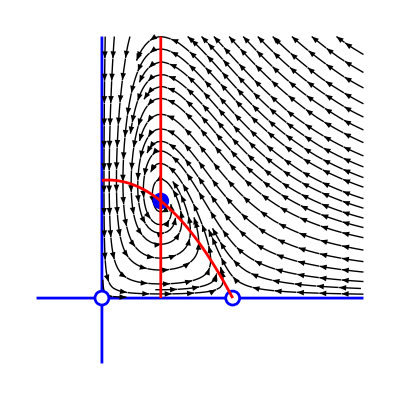

```mathematica
gr02=ParametricPlot[{{t,0},{0,t}},{t,-0.5,2},PlotStyle->{{Blue,Thickness[0.005]},{Blue,Thickness[0.005]}},Axes->False]; (*Ejes*)
gr2=StreamPlot[{F2[u,v],G2[u,v]},{u,0,2},{v,0,2},StreamStyle->Black]; (*Campos vectoriales*)
gr21=ListPlot[{P21,P22,P23},PlotStyle-> {PointSize[0.03],Blue}];
gr22=ListPlot[{P21,P22},PlotStyle-> {PointSize[0.02],White}];
gr23 = ParametricPlot[{0.45,t},{t,0,2},PlotStyle->{Red,Thickness[0.005]}]; (*Campo vertical*)
gr24 = ParametricPlot[{t,(1-t)*(0.9+t)},{t,0,1},PlotStyle->{Red,Thickness[0.005]}];(*Campo horizontal*)
Show[gr02,gr2,gr21,gr22,gr23,gr24]
```

## CASO 3

Ejemplo cuando C < M/(1 + B)  y P3 es inestable:

```mathematica
F3[u_,v_]=u(1-u-v/(u+0.25));
G3[u_,v_]=v(-1+3*u/(u+0.25));
equilibrio3=Solve[{F3[u,v]==0,G3[u,v]==0},{u,v}];
P31={u,v}/.equilibrio3[[3]];
P32={u,v}/.equilibrio3[[2]];
P33={u,v}/.equilibrio3[[1]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

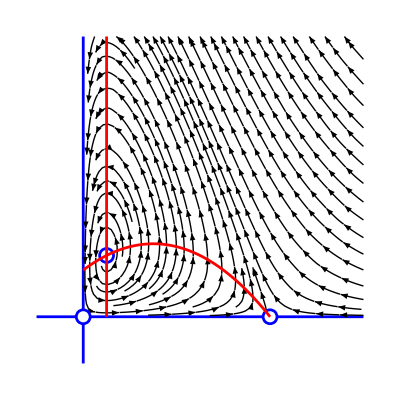

```mathematica
gr03=ParametricPlot[{{t,0},{0,t}},{t,-0.25,1.5},PlotStyle->{{Blue,Thickness[0.005]},{Blue,Thickness[0.005]}},Axes->False]; (*Ejes*)
gr3=StreamPlot[{F3[u,v],G3[u,v]},{u,0,1.5},{v,0,1.5},StreamStyle->Black]; (*Campos vectoriales*)
gr31=ListPlot[{P31,P32,P33},PlotStyle-> {PointSize[0.03],Blue}];
gr32=ListPlot[{P31,P32,P33},PlotStyle-> {PointSize[0.02],White}];
gr33 = ParametricPlot[{0.125,t},{t,0,1.5},PlotStyle->{Red,Thickness[0.005]}]; (*Campo vertical*)
gr34 = ParametricPlot[{t,(1-t)*(0.25+t)},{t,0,1},PlotStyle->{Red,Thickness[0.005]}]; (*Campo horizontal*)
Show[gr03,gr3,gr31,gr32,gr33,gr34]
```